# Dedekind number

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

```mathematica
WikipediaData["Dedekind number","SummaryPlaintext"]
```

In mathematics, the Dedekind numbers are a rapidly growing sequence of integers named after Richard Dedekind, who defined them in 1897. The Dedekind number M(n) counts the number of monotone boolean functions of n variables. Equivalently, it counts the number of antichains of subsets of an n-element set, the number of elements in a free distributive lattice with n generators, or one more than the number of abstract simplicial complexes on a set with n elements.
Accurate asymptotic estimates of M(n) and an exact expression as a summation are known. However Dedekind's problem of computing the values of M(n) remains difficult: no closed-form expression for M(n) is known, and exact values of M(n) have been found only for n ≤ 9.(sequence A000372 in the OEIS)

```mathematica
WikipediaData["Dedekind number","ArticlePlaintext"]
```

In mathematics, the Dedekind numbers are a rapidly growing sequence of integers named after Richard Dedekind, who defined them in 1897. The Dedekind number M(n) counts the number of monotone boolean functions of n variables. Equivalently, it counts the number of antichains of subsets of an n-element set, the number of elements in a free distributive lattice with n generators, or one more than the number of abstract simplicial complexes on a set with n elements.
Accurate asymptotic estimates of M(n) and an exact expression as a summation are known. However Dedekind's problem of computing the values of M(n) remains difficult: no closed-form expression for M(n) is known, and exact values of M(n) have been found only for n ≤ 9.(sequence A000372 in the OEIS)


== Definitions ==
A Boolean function is a function that takes as input n Boolean variables (that is, values that can be either false or true, or equivalently binary values that can be either 0 or 1), and produces as output another Boolean variable. It is monotonic if, for every combination of inputs, switching one of the inputs from false to true can only cause the output to switch from false to true and not from true to false. The Dedekind number M(n) is the number of different monotonic Boolean functions on n variables.An antichain of sets (also known as a Sperner family) is a family of sets, none of which is contained in any other set. If V is a set of n Boolean variables, an antichain A of subsets of V defines a monotone Boolean function f, where the value of f is true for a given set of inputs if some subset of the true inputs to f belongs to A and false otherwise. Conversely every monotone Boolean function defines in this way an antichain, of the minimal subsets of Boolean variables that can force the function value to be true. Therefore, the Dedekind number M(n) equals the number of different antichains of subsets of an n-element set.A third, equivalent way of describing the same class of objects uses lattice theory. From any two monotone Boolean functions f and g we can find two other monotone Boolean functions f ∧ g and f ∨ g, their logical conjunction and logical disjunction respectively. The family of all monotone Boolean functions on n inputs, together with these two operations, forms a distributive lattice, the lattice given by Birkhoff's representation theorem from the partially ordered set of subsets of the n variables with set inclusion as the partial order. This construction produces the free distributive lattice with n generators. Thus, the Dedekind numbers count the number of elements in free distributive lattices.The Dedekind numbers also count one more than the number of abstract simplicial complexes on a set with n elements, families of sets with the property that any non-empty subset of a set in the family also belongs to the family. Any antichain (except {Ø}) determines a simplicial complex, the family of subsets of antichain members, and conversely the maximal simplices in a complex form an antichain.


== Example ==
For n = 2, there are six monotonic Boolean functions and six antichains of subsets of the two-element set {x,y}:

The function f(x,y) = false that ignores its input values and always returns false corresponds to the empty antichain Ø.
The logical conjunction f(x,y) = x ∧ y corresponds to the antichain { {x,y} } containing the single set {x,y}.
The function f(x,y) = x that ignores its second argument and returns the first argument corresponds to the antichain { {x} } containing the single set {x}
The function f(x,y) = y that ignores its first argument and returns the second argument corresponds to the antichain { {y} } containing the single set {y}
The logical disjunction f(x,y) = x ∨ y corresponds to the antichain { {x}, {y} } containing the two sets {x} and {y}.
The function f(x,y) = true that ignores its input values and always returns true corresponds to the antichain {Ø} containing only the empty set.


== Values ==
The exact values of the Dedekind numbers are known for 0 ≤ n ≤ 9:

2, 3, 6, 20, 168, 7581, 7828354, 2414682040998, 56130437228687557907788, 286386577668298411128469151667598498812366 (sequence A000372 in the OEIS).The first six of these numbers are given by Church (1940). M(6) was calculated by Ward (1946), M(7) was calculated by Church (1965) and Berman & Köhler (1976), M(8) by Wiedemann (1991) and M(9) was simultaneously discovered in 2023 by Christian Jäkel and Lennart Van Hirtum et al.If n is even, then M(n) must also be even.
The calculation of the fifth Dedekind number M(5) = 7581 disproved a conjecture by Garrett Birkhoff that M(n) is always divisible by (2n − 1)(2n − 2).


== Summation formula ==
Kisielewicz (1988) rewrote the logical definition of antichains into the following arithmetic formula for the Dedekind numbers:

  
    
      
        M
        (
        n
        )
        =
        
          ∑
          
            k
            =
            1
          
          
            
              2
              
                
                  2
                  
                    n
                  
                
              
            
          
        
        
          ∏
          
            j
            =
            1
          
          
            
              2
              
                n
              
            
            −
            1
          
        
        
          ∏
          
            i
            =
            0
          
          
            j
            −
            1
          
        
        
          (
          
            1
            −
            
              b
              
                i
              
              
                k
              
            
            
              b
              
                j
              
              
                k
              
            
            
              ∏
              
                m
                =
                0
              
              
                
                  log
                  
                    2
                  
                
                ⁡
                i
              
            
            (
            1
            −
            
              b
              
                m
              
              
                i
              
            
            +
            
              b
              
                m
              
              
                i
              
            
            
              b
              
                m
              
              
                j
              
            
            )
          
          )
        
        ,
      
    
    {\displaystyle M(n)=\sum _{k=1}^{2^{2^{n}}}\prod _{j=1}^{2^{n}-1}\prod _{i=0}^{j-1}\left(1-b_{i}^{k}b_{j}^{k}\prod _{m=0}^{\log _{2}i}(1-b_{m}^{i}+b_{m}^{i}b_{m}^{j})\right),}
  where 
  
    
      
        
          b
          
            i
          
          
            k
          
        
      
    
    {\displaystyle b_{i}^{k}}
   is the 
  
    
      
        i
      
    
    {\displaystyle i}
  th bit of the number 
  
    
      
        k
      
    
    {\displaystyle k}
  ,
which can be written using the floor function as

  
    
      
        
          b
          
            i
          
          
            k
          
        
        =
        
          ⌊
          
            
              k
              
                2
                
                  i
                
              
            
          
          ⌋
        
        −
        2
        
          ⌊
          
            
              k
              
                2
                
                  i
                  +
                  1
                
              
            
          
          ⌋
        
        .
      
    
    {\displaystyle b_{i}^{k}=\left\lfloor {\frac {k}{2^{i}}}\right\rfloor -2\left\lfloor {\frac {k}{2^{i+1}}}\right\rfloor .}
  However, this formula is not helpful for computing the values of M(n) for large n due to the large number of terms in the summation.


== Asymptotics ==
The logarithm of the Dedekind numbers can be estimated accurately via the bounds

  
    
      
        
          
            
              (
            
            
              n
              
                ⌊
                n
                
                  /
                
                2
                ⌋
              
            
            
              )
            
          
        
        ≤
        
          log
          
            2
          
        
        ⁡
        M
        (
        n
        )
        ≤
        
          
            
              (
            
            
              n
              
                ⌊
                n
                
                  /
                
                2
                ⌋
              
            
            
              )
            
          
        
        
          (
          
            1
            +
            O
            
              (
              
                
                  
                    log
                    ⁡
                    n
                  
                  n
                
              
              )
            
          
          )
        
        .
      
    
    {\displaystyle {n \choose \lfloor n/2\rfloor }\leq \log _{2}M(n)\leq {n \choose \lfloor n/2\rfloor }\left(1+O\left({\frac {\log n}{n}}\right)\right).}
  Here the left inequality counts the number of antichains in which each set has exactly 
  
    
      
        ⌊
        n
        
          /
        
        2
        ⌋
      
    
    {\displaystyle \lfloor n/2\rfloor }
   elements, and the right inequality was proven by Kleitman & Markowsky (1975).
Korshunov (1981) provided the even more accurate estimates

  
    
      
        M
        (
        n
        )
        =
        (
        1
        +
        o
        (
        1
        )
        )
        
          2
          
            
              
                (
              
              
                n
                
                  ⌊
                  n
                  
                    /
                  
                  2
                  ⌋
                
              
              
                )
              
            
          
        
        exp
        ⁡
        a
        (
        n
        )
      
    
    {\displaystyle M(n)=(1+o(1))2^{n \choose \lfloor n/2\rfloor }\exp a(n)}
  for even n, and

  
    
      
        M
        (
        n
        )
        =
        (
        1
        +
        o
        (
        1
        )
        )
        
          2
          
            
              
                
                  (
                
                
                  n
                  
                    ⌊
                    n
                    
                      /
                    
                    2
                    ⌋
                  
                
                
                  )
                
              
            
            +
            1
          
        
        exp
        ⁡
        (
        b
        (
        n
        )
        +
        c
        (
        n
        )
        )
      
    
    {\displaystyle M(n)=(1+o(1))2^{{n \choose \lfloor n/2\rfloor }+1}\exp(b(n)+c(n))}
  for odd n, where

  
    
      
        a
        (
        n
        )
        =
        
          
            
              (
            
            
              n
              
                n
                
                  /
                
                2
                −
                1
              
            
            
              )
            
          
        
        (
        
          2
          
            −
            n
            
              /
            
            2
          
        
        +
        
          n
          
            2
          
        
        
          2
          
            −
            n
            −
            5
          
        
        −
        n
        
          2
          
            −
            n
            −
            4
          
        
        )
        ,
      
    
    {\displaystyle a(n)={n \choose n/2-1}(2^{-n/2}+n^{2}2^{-n-5}-n2^{-n-4}),}
  

  
    
      
        b
        (
        n
        )
        =
        
          
            
              (
            
            
              n
              
                (
                n
                −
                3
                )
                
                  /
                
                2
              
            
            
              )
            
          
        
        (
        
          2
          
            −
            (
            n
            +
            3
            )
            
              /
            
            2
          
        
        +
        
          n
          
            2
          
        
        
          2
          
            −
            n
            −
            6
          
        
        −
        n
        
          2
          
            −
            n
            −
            3
          
        
        )
        ,
      
    
    {\displaystyle b(n)={n \choose (n-3)/2}(2^{-(n+3)/2}+n^{2}2^{-n-6}-n2^{-n-3}),}
  and

  
    
      
        c
        (
        n
        )
        =
        
          
            
              (
            
            
              n
              
                (
                n
                −
                1
                )
                
                  /
                
                2
              
            
            
              )
            
          
        
        (
        
          2
          
            −
            (
            n
            +
            1
            )
            
              /
            
            2
          
        
        +
        
          n
          
            2
          
        
        
          2
          
            −
            n
            −
            4
          
        
        )
        .
      
    
    {\displaystyle c(n)={n \choose (n-1)/2}(2^{-(n+1)/2}+n^{2}2^{-n-4}).}
  The main idea behind these estimates is that, in most antichains, all the sets have sizes that are very close to n/2. For n = 2, 4, 6, 8 Korshunov's formula provides an estimate that is inaccurate by a factor of 9.8%, 10.2%, 4.1%, and −3.3%, respectively.


== Notes ==


== References ==
Berman, Joel; Köhler, Peter (1976), "Cardinalities of finite distributive lattices", Mitt. Math. Sem. Giessen, 121: 103–124, MR 0485609.
Church, Randolph (1940), "Numerical analysis of certain free distributive structures", Duke Mathematical Journal, 6 (3): 732–734, doi:10.1215/s0012-7094-40-00655-x, MR 0002842.
Church, Randolph (1965), "Enumeration by rank of the free distributive lattice with 7 generators", Notices of the American Mathematical Society, 11: 724. As cited by Wiedemann (1991).
Dedekind, Richard (1897), "Über Zerlegungen von Zahlen durch ihre größten gemeinsamen Teiler", Gesammelte Werke, vol. 2, pp. 103–148.
Kahn, Jeff (2002), "Entropy, independent sets and antichains: a new approach to Dedekind's problem", Proceedings of the American Mathematical Society, 130 (2): 371–378, doi:10.1090/S0002-9939-01-06058-0, MR 1862115.
Kisielewicz, Andrzej (1988), "A solution of Dedekind's problem on the number of isotone Boolean functions", Journal für die Reine und Angewandte Mathematik, 1988 (386): 139–144, doi:10.1515/crll.1988.386.139, MR 0936995, S2CID 115293297
Kleitman, D.; Markowsky, G. (1975), "On Dedekind's problem: the number of isotone Boolean functions. II", Transactions of the American Mathematical Society, 213: 373–390, doi:10.2307/1998052, JSTOR 1998052, MR 0382107.
Korshunov, A. D. (1981), "The number of monotone Boolean functions", Problemy Kibernet., 38: 5–108, MR 0640855.
Ward, Morgan (1946), "Note on the order of free distributive lattices", Bulletin of the American Mathematical Society, 52: 423, doi:10.1090/S0002-9904-1946-08568-7.
Wiedemann, Doug (1991), "A computation of the eighth Dedekind number", Order, 8 (1): 5–6, doi:10.1007/BF00385808, MR 1129608, S2CID 120878757.
Yamamoto, Koichi (1953), "Note on the order of free distributive lattices", Science Reports of the Kanazawa University, 2 (1): 5–6, MR 0070608.
Zaguia, Nejib (1993), "Isotone maps: enumeration and structure", in Sauer, N. W.; Woodrow, R. E.; Sands, B. (eds.), Finite and Infinite Combinatorics in Sets and Logic (Proc. NATO Advanced Study Inst., Banff, Alberta, Canada, May 4, 1991), Kluwer Academic Publishers, pp. 421–430, MR 1261220.

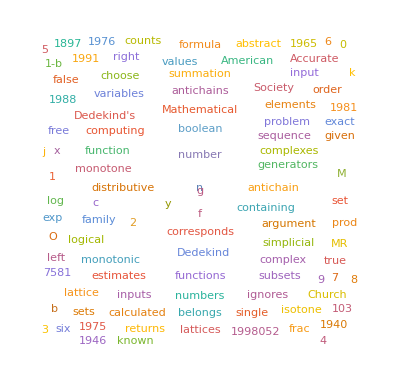

```mathematica
WordCloud[DeleteStopwords@Select[DictionaryWordQ]@TextWords[WikipediaData["Dedekind number","ArticlePlaintext"]]]
```

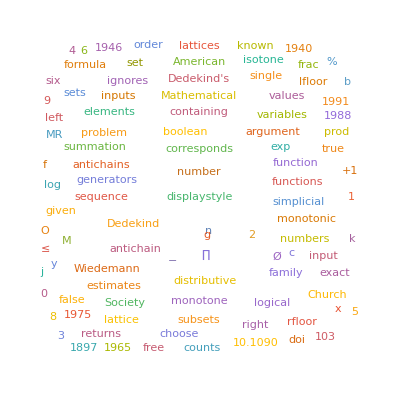

```mathematica
WordCloud[DeleteStopwords@WikipediaData["Dedekind number","ArticlePlaintext"]]
```

```mathematica
ResourceFunction["OEISSequence"]["A000372"]
```

{2,3,6,20,168,7581,7828354,2414682040998,56130437228687557907788,286386577668298411128469151667598498812366}

```mathematica
Dataset[AssociationThread[Range[0,9]->ResourceFunction["OEISSequence"]["A000372"]]]
```

```mathematica
ResourceFunction["EchoPerformance"][nn=5;
stableSets[u_,Q_]:=If[Length[u]===0,{{}},With[{w=First[u]},Join[stableSets[DeleteCases[u,w],Q],Prepend[#,w]&/@stableSets[DeleteCases[u,r_/;r===w||Q[r,w]||Q[w,r]],Q]]]];
Table[Length[stableSets[Subsets[Range[n]],SubsetQ]],{n,0,nn}] (*Gus Wiseman,Feb 20 2019*)]
```

CompoundExpression  {0.590194 s,811576 B}

{2,3,6,20,168,7581}

```mathematica
ResourceFunction["EchoPerformance"][Table[Total[Boole[Table[UnateQ[BooleanFunction[k,n]],{k,0,2^(2^n)-1}]]],{n,0,4}] (*Eric W.Weisstein,Jun 27 2023*)]
```

Table  {4.07275 s,13420768 B}

{2,3,6,20,168}

```mathematica
WikipediaData["Dedekind number","ImageDataset"]
```

```mathematica
WikipediaData["Dedekind number","ImageList"]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
WikipediaData["Dedekind number","ImageURLs"]
```

{https://commons.wikimedia.org/wiki/File:Loupe_light.svg,https://commons.wikimedia.org/wiki/File:Monotone_Boolean_functions_0,1,2,3.svg,https://en.wikipedia.org/wiki/File:Symbol_portal_class.svg}

```mathematica
URL/@WikipediaData["Dedekind number","ImageURLs"]
```

{URL[https://commons.wikimedia.org/wiki/File:Loupe_light.svg],URL[https://commons.wikimedia.org/wiki/File:Monotone_Boolean_functions_0,1,2,3.svg],URL[https://en.wikipedia.org/wiki/File:Symbol_portal_class.svg]}

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

PeterBurbery/Combinatorics

PeterBurbery`Combinatorics`

PeterBurbery/Combinatorics/tutorial/Dedekindnumber

### Keywords